```mathematica
values2=With[
{step=100, base=10},
Table[
With[
{a=Timing[{exp,exp+step,AlgoList3[base^exp,base^(exp+step),{3,5,7,11}]}]},
Print[a];Last[Last[Last[a]]]],
{exp,68000,106900,step}
]
]
```

{0.015,{68000,68100,{{3,5,7,11},{},1068}}}

{0.,{68100,68200,{{3,5,7,11},{},980}}}

{0.,{68200,68300,{{3,5,7,11},{},971}}}

{0.016,{68300,68400,{{3,5,7,11},{},952}}}

{0.,{68400,68500,{{3,5,7,11},{},1019}}}

{0.016,{68500,68600,{{3,5,7,11},{},1025}}}

{0.,{68600,68700,{{3,5,7,11},{},924}}}

{0.,{68700,68800,{{3,5,7,11},{},1132}}}

{0.015,{68800,68900,{{3,5,7,11},{},955}}}

{0.,{68900,69000,{{3,5,7,11},{},1062}}}

{0.016,{69000,69100,{{3,5,7,11},{},1003}}}

{2.84501×10^-11,{69100,69200,{{3,5,7,11},{},1071}}}

{0.015,{69200,69300,{{3,5,7,11},{},975}}}

{1.44667×10^-11,{69300,69400,{{3,5,7,11},{},1029}}}

{0.016,{69400,69500,{{3,5,7,11},{},951}}}

{1.11982×10^-11,{69500,69600,{{3,5,7,11},{},969}}}

{0.016,{69600,69700,{{3,5,7,11},{},926}}}

{7.95808×10^-12,{69700,69800,{{3,5,7,11},{},905}}}

{0.015,{69800,69900,{{3,5,7,11},{},934}}}

{0.,{69900,70000,{{3,5,7,11},{},987}}}

{0.,{70000,70100,{{3,5,7,11},{},1150}}}

{0.016,{70100,70200,{{3,5,7,11},{},941}}}

{0.,{70200,70300,{{3,5,7,11},{},1065}}}

{0.015,{70300,70400,{{3,5,7,11},{},966}}}

{0.,{70400,70500,{{3,5,7,11},{},894}}}

{0.016,{70500,70600,{{3,5,7,11},{},967}}}

{0.,{70600,70700,{{3,5,7,11},{},873}}}

{0.016,{70700,70800,{{3,5,7,11},{},882}}}

{0.015,{70800,70900,{{3,5,7,11},{},901}}}

{1.44667×10^-11,{70900,71000,{{3,5,7,11},{},1045}}}

{1.44667×10^-11,{71000,71100,{{3,5,7,11},{},984}}}

{0.016,{71100,71200,{{3,5,7,11},{},1073}}}

{1.11982×10^-11,{71200,71300,{{3,5,7,11},{},1074}}}

{0.015,{71300,71400,{{3,5,7,11},{},1078}}}

{0.,{71400,71500,{{3,5,7,11},{},1042}}}

{0.016,{71500,71600,{{3,5,7,11},{},932}}}

{0.,{71600,71700,{{3,5,7,11},{},925}}}

{0.016,{71700,71800,{{3,5,7,11},{},970}}}

{0.,{71800,71900,{{3,5,7,11},{},941}}}

{0.015,{71900,72000,{{3,5,7,11},{},1017}}}

{0.,{72000,72100,{{3,5,7,11},{},942}}}

{0.016,{72100,72200,{{3,5,7,11},{},941}}}

{0.,{72200,72300,{{3,5,7,11},{},900}}}

{0.015,{72300,72400,{{3,5,7,11},{},959}}}

{1.77351×10^-11,{72400,72500,{{3,5,7,11},{},905}}}

{1.77351×10^-11,{72500,72600,{{3,5,7,11},{},923}}}

{0.016,{72600,72700,{{3,5,7,11},{},939}}}

{1.44667×10^-11,{72700,72800,{{3,5,7,11},{},1137}}}

{0.016,{72800,72900,{{3,5,7,11},{},1037}}}

{0.015,{72900,73000,{{3,5,7,11},{},1029}}}

{0.,{73000,73100,{{3,5,7,11},{},1051}}}

{0.016,{73100,73200,{{3,5,7,11},{},1010}}}

{0.,{73200,73300,{{3,5,7,11},{},1021}}}

{0.015,{73300,73400,{{3,5,7,11},{},984}}}

{0.,{73400,73500,{{3,5,7,11},{},989}}}

{0.016,{73500,73600,{{3,5,7,11},{},973}}}

{0.,{73600,73700,{{3,5,7,11},{},915}}}

{0.016,{73700,73800,{{3,5,7,11},{},1015}}}

{0.,{73800,73900,{{3,5,7,11},{},1031}}}

{0.015,{73900,74000,{{3,5,7,11},{},989}}}

{1.77351×10^-11,{74000,74100,{{3,5,7,11},{},960}}}

{0.016,{74100,74200,{{3,5,7,11},{},1000}}}

{1.44667×10^-11,{74200,74300,{{3,5,7,11},{},949}}}

{0.015,{74300,74400,{{3,5,7,11},{},934}}}

{0.016,{74400,74500,{{3,5,7,11},{},951}}}

{0.,{74500,74600,{{3,5,7,11},{},912}}}

{0.016,{74600,74700,{{3,5,7,11},{},1043}}}

{0.,{74700,74800,{{3,5,7,11},{},916}}}

{0.015,{74800,74900,{{3,5,7,11},{},1009}}}

{0.016,{74900,75000,{{3,5,7,11},{},986}}}

{0.,{75000,75100,{{3,5,7,11},{},1084}}}

{0.015,{75100,75200,{{3,5,7,11},{},1077}}}

{0.016,{75200,75300,{{3,5,7,11},{},1006}}}

{1.77351×10^-11,{75300,75400,{{3,5,7,11},{},848}}}

{1.77351×10^-11,{75400,75500,{{3,5,7,11},{},1008}}}

{0.016,{75500,75600,{{3,5,7,11},{},852}}}

{1.44667×10^-11,{75600,75700,{{3,5,7,11},{},1002}}}

{0.015,{75700,75800,{{3,5,7,11},{},1035}}}

{5.11591×10^-13,{75800,75900,{{3,5,7,11},{},940}}}

{0.016,{75900,76000,{{3,5,7,11},{},1044}}}

{0.015,{76000,76100,{{3,5,7,11},{},980}}}

{0.,{76100,76200,{{3,5,7,11},{},969}}}

{0.016,{76200,76300,{{3,5,7,11},{},958}}}

{0.,{76300,76400,{{3,5,7,11},{},948}}}

{0.016,{76400,76500,{{3,5,7,11},{},932}}}

{0.,{76500,76600,{{3,5,7,11},{},967}}}

{0.015,{76600,76700,{{3,5,7,11},{},973}}}

{2.10036×10^-11,{76700,76800,{{3,5,7,11},{},850}}}

{0.016,{76800,76900,{{3,5,7,11},{},1177}}}

{1.77351×10^-11,{76900,77000,{{3,5,7,11},{},942}}}

{0.015,{77000,77100,{{3,5,7,11},{},940}}}

{3.75167×10^-12,{77100,77200,{{3,5,7,11},{},939}}}

{0.016,{77200,77300,{{3,5,7,11},{},969}}}

{5.11591×10^-13,{77300,77400,{{3,5,7,11},{},806}}}

{0.016,{77400,77500,{{3,5,7,11},{},1023}}}

{0.,{77500,77600,{{3,5,7,11},{},1021}}}

{0.015,{77600,77700,{{3,5,7,11},{},860}}}

{0.,{77700,77800,{{3,5,7,11},{},1033}}}

{0.016,{77800,77900,{{3,5,7,11},{},1015}}}

{0.,{77900,78000,{{3,5,7,11},{},992}}}

{0.015,{78000,78100,{{3,5,7,11},{},1140}}}

{2.42437×10^-11,{78100,78200,{{3,5,7,11},{},987}}}

{0.016,{78200,78300,{{3,5,7,11},{},980}}}

{2.10036×10^-11,{78300,78400,{{3,5,7,11},{},904}}}

{0.016,{78400,78500,{{3,5,7,11},{},1069}}}

{0.015,{78500,78600,{{3,5,7,11},{},993}}}

{3.75167×10^-12,{78600,78700,{{3,5,7,11},{},1006}}}

{0.016,{78700,78800,{{3,5,7,11},{},1014}}}

{5.11591×10^-13,{78800,78900,{{3,5,7,11},{},1047}}}

{0.015,{78900,79000,{{3,5,7,11},{},1004}}}

{0.016,{79000,79100,{{3,5,7,11},{},1048}}}

{0.,{79100,79200,{{3,5,7,11},{},889}}}

{0.016,{79200,79300,{{3,5,7,11},{},1057}}}

{0.,{79300,79400,{{3,5,7,11},{},993}}}

{0.015,{79400,79500,{{3,5,7,11},{},1080}}}

{2.42437×10^-11,{79500,79600,{{3,5,7,11},{},1027}}}

{0.016,{79600,79700,{{3,5,7,11},{},1097}}}

{0.015,{79700,79800,{{3,5,7,11},{},954}}}

{7.02016×10^-12,{79800,79900,{{3,5,7,11},{},1081}}}

{0.016,{79900,80000,{{3,5,7,11},{},944}}}

{3.75167×10^-12,{80000,80100,{{3,5,7,11},{},965}}}

{0.016,{80100,80200,{{3,5,7,11},{},940}}}

{0.015,{80200,80300,{{3,5,7,11},{},1011}}}

{0.,{80300,80400,{{3,5,7,11},{},927}}}

{0.016,{80400,80500,{{3,5,7,11},{},982}}}

{0.,{80500,80600,{{3,5,7,11},{},1020}}}

{0.015,{80600,80700,{{3,5,7,11},{},938}}}

{0.016,{80700,80800,{{3,5,7,11},{},991}}}

{2.42437×10^-11,{80800,80900,{{3,5,7,11},{},1104}}}

{0.016,{80900,81000,{{3,5,7,11},{},960}}}

{0.015,{81000,81100,{{3,5,7,11},{},956}}}

{7.02016×10^-12,{81100,81200,{{3,5,7,11},{},1029}}}

{0.016,{81200,81300,{{3,5,7,11},{},993}}}

{3.75167×10^-12,{81300,81400,{{3,5,7,11},{},928}}}

{0.015,{81400,81500,{{3,5,7,11},{},954}}}

{0.016,{81500,81600,{{3,5,7,11},{},1036}}}

{0.,{81600,81700,{{3,5,7,11},{},963}}}

{0.016,{81700,81800,{{3,5,7,11},{},1008}}}

{0.015,{81800,81900,{{3,5,7,11},{},1044}}}

{2.75122×10^-11,{81900,82000,{{3,5,7,11},{},1000}}}

{0.016,{82000,82100,{{3,5,7,11},{},962}}}

{0.015,{82100,82200,{{3,5,7,11},{},916}}}

{1.02887×10^-11,{82200,82300,{{3,5,7,11},{},954}}}

{0.016,{82300,82400,{{3,5,7,11},{},1042}}}

{7.02016×10^-12,{82400,82500,{{3,5,7,11},{},972}}}

{0.016,{82500,82600,{{3,5,7,11},{},1007}}}

{0.015,{82600,82700,{{3,5,7,11},{},1031}}}

{0.,{82700,82800,{{3,5,7,11},{},1015}}}

{0.016,{82800,82900,{{3,5,7,11},{},1102}}}

{0.,{82900,83000,{{3,5,7,11},{},1033}}}

{0.015,{83000,83100,{{3,5,7,11},{},1027}}}

{0.,{83100,83200,{{3,5,7,11},{},1003}}}

{0.016,{83200,83300,{{3,5,7,11},{},1038}}}

{2.75122×10^-11,{83300,83400,{{3,5,7,11},{},1073}}}

{0.016,{83400,83500,{{3,5,7,11},{},937}}}

{0.015,{83500,83600,{{3,5,7,11},{},991}}}

{1.02887×10^-11,{83600,83700,{{3,5,7,11},{},1031}}}

{0.016,{83700,83800,{{3,5,7,11},{},982}}}

{0.015,{83800,83900,{{3,5,7,11},{},931}}}

{0.,{83900,84000,{{3,5,7,11},{},895}}}

{0.016,{84000,84100,{{3,5,7,11},{},935}}}

{0.016,{84100,84200,{{3,5,7,11},{},993}}}

{0.,{84200,84300,{{3,5,7,11},{},923}}}

{0.015,{84300,84400,{{3,5,7,11},{},1102}}}

{0.,{84400,84500,{{3,5,7,11},{},1082}}}

{0.016,{84500,84600,{{3,5,7,11},{},1012}}}

{0.015,{84600,84700,{{3,5,7,11},{},916}}}

{1.35287×10^-11,{84700,84800,{{3,5,7,11},{},1057}}}

{0.016,{84800,84900,{{3,5,7,11},{},861}}}

{1.02887×10^-11,{84900,85000,{{3,5,7,11},{},936}}}

{0.016,{85000,85100,{{3,5,7,11},{},883}}}

{0.015,{85100,85200,{{3,5,7,11},{},826}}}

{0.,{85200,85300,{{3,5,7,11},{},953}}}

{0.016,{85300,85400,{{3,5,7,11},{},1141}}}

{0.015,{85400,85500,{{3,5,7,11},{},1003}}}

{0.,{85500,85600,{{3,5,7,11},{},1058}}}

{0.016,{85600,85700,{{3,5,7,11},{},920}}}

{0.016,{85700,85800,{{3,5,7,11},{},1073}}}

{2.75122×10^-11,{85800,85900,{{3,5,7,11},{},1013}}}

{0.015,{85900,86000,{{3,5,7,11},{},1042}}}

{0.016,{86000,86100,{{3,5,7,11},{},911}}}

{0.015,{86100,86200,{{3,5,7,11},{},1062}}}

{0.,{86200,86300,{{3,5,7,11},{},940}}}

{0.016,{86300,86400,{{3,5,7,11},{},938}}}

{0.016,{86400,86500,{{3,5,7,11},{},927}}}

{0.,{86500,86600,{{3,5,7,11},{},996}}}

{0.015,{86600,86700,{{3,5,7,11},{},985}}}

{0.016,{86700,86800,{{3,5,7,11},{},971}}}

{0.,{86800,86900,{{3,5,7,11},{},916}}}

{0.015,{86900,87000,{{3,5,7,11},{},967}}}

{0.016,{87000,87100,{{3,5,7,11},{},952}}}

{0.016,{87100,87200,{{3,5,7,11},{},970}}}

{1.02887×10^-11,{87200,87300,{{3,5,7,11},{},1095}}}

{0.015,{87300,87400,{{3,5,7,11},{},966}}}

{0.,{87400,87500,{{3,5,7,11},{},1022}}}

{0.016,{87500,87600,{{3,5,7,11},{},981}}}

{0.015,{87600,87700,{{3,5,7,11},{},931}}}

{0.,{87700,87800,{{3,5,7,11},{},1045}}}

{0.016,{87800,87900,{{3,5,7,11},{},897}}}

{0.016,{87900,88000,{{3,5,7,11},{},881}}}

{0.,{88000,88100,{{3,5,7,11},{},960}}}

{0.015,{88100,88200,{{3,5,7,11},{},911}}}

{0.016,{88200,88300,{{3,5,7,11},{},947}}}

{1.35287×10^-11,{88300,88400,{{3,5,7,11},{},1070}}}

{0.015,{88400,88500,{{3,5,7,11},{},1022}}}

{0.016,{88500,88600,{{3,5,7,11},{},1004}}}

{0.,{88600,88700,{{3,5,7,11},{},985}}}

{0.016,{88700,88800,{{3,5,7,11},{},923}}}

{0.015,{88800,88900,{{3,5,7,11},{},992}}}

{0.016,{88900,89000,{{3,5,7,11},{},997}}}

{0.015,{89000,89100,{{3,5,7,11},{},962}}}

{2.00657×10^-11,{89100,89200,{{3,5,7,11},{},946}}}

{0.016,{89200,89300,{{3,5,7,11},{},910}}}

{0.016,{89300,89400,{{3,5,7,11},{},985}}}

{1.35287×10^-11,{89400,89500,{{3,5,7,11},{},986}}}

{0.015,{89500,89600,{{3,5,7,11},{},1009}}}

{0.,{89600,89700,{{3,5,7,11},{},952}}}

{0.016,{89700,89800,{{3,5,7,11},{},855}}}

{0.015,{89800,89900,{{3,5,7,11},{},1027}}}

{0.,{89900,90000,{{3,5,7,11},{},965}}}

{0.016,{90000,90100,{{3,5,7,11},{},977}}}

{0.016,{90100,90200,{{3,5,7,11},{},977}}}

{0.015,{90200,90300,{{3,5,7,11},{},960}}}

{0.016,{90300,90400,{{3,5,7,11},{},1034}}}

{0.015,{90400,90500,{{3,5,7,11},{},1037}}}

{2.84217×10^-12,{90500,90600,{{3,5,7,11},{},935}}}

{0.016,{90600,90700,{{3,5,7,11},{},926}}}

{0.016,{90700,90800,{{3,5,7,11},{},1018}}}

{0.,{90800,90900,{{3,5,7,11},{},960}}}

{0.015,{90900,91000,{{3,5,7,11},{},895}}}

{0.016,{91000,91100,{{3,5,7,11},{},977}}}

{0.015,{91100,91200,{{3,5,7,11},{},1104}}}

{0.016,{91200,91300,{{3,5,7,11},{},919}}}

{2.00657×10^-11,{91300,91400,{{3,5,7,11},{},1054}}}

{0.016,{91400,91500,{{3,5,7,11},{},1023}}}

{0.015,{91500,91600,{{3,5,7,11},{},1002}}}

{0.016,{91600,91700,{{3,5,7,11},{},1045}}}

{0.,{91700,91800,{{3,5,7,11},{},964}}}

{0.015,{91800,91900,{{3,5,7,11},{},1002}}}

{0.016,{91900,92000,{{3,5,7,11},{},927}}}

{0.016,{92000,92100,{{3,5,7,11},{},1032}}}

{0.,{92100,92200,{{3,5,7,11},{},1004}}}

{0.015,{92200,92300,{{3,5,7,11},{},1145}}}

{2.33058×10^-11,{92300,92400,{{3,5,7,11},{},955}}}

{0.016,{92400,92500,{{3,5,7,11},{},999}}}

{0.015,{92500,92600,{{3,5,7,11},{},1083}}}

{6.08225×10^-12,{92600,92700,{{3,5,7,11},{},1097}}}

{0.016,{92700,92800,{{3,5,7,11},{},971}}}

{0.016,{92800,92900,{{3,5,7,11},{},953}}}

{0.,{92900,93000,{{3,5,7,11},{},919}}}

{0.015,{93000,93100,{{3,5,7,11},{},927}}}

{0.016,{93100,93200,{{3,5,7,11},{},976}}}

{0.,{93200,93300,{{3,5,7,11},{},1035}}}

{0.015,{93300,93400,{{3,5,7,11},{},943}}}

{0.016,{93400,93500,{{3,5,7,11},{},1054}}}

{2.33058×10^-11,{93500,93600,{{3,5,7,11},{},917}}}

{0.016,{93600,93700,{{3,5,7,11},{},1077}}}

{2.00657×10^-11,{93700,93800,{{3,5,7,11},{},983}}}

{0.015,{93800,93900,{{3,5,7,11},{},933}}}

{0.016,{93900,94000,{{3,5,7,11},{},876}}}

{0.015,{94000,94100,{{3,5,7,11},{},1025}}}

{0.,{94100,94200,{{3,5,7,11},{},885}}}

{0.016,{94200,94300,{{3,5,7,11},{},1030}}}

{0.016,{94300,94400,{{3,5,7,11},{},1029}}}

{0.015,{94400,94500,{{3,5,7,11},{},1049}}}

{2.65743×10^-11,{94500,94600,{{3,5,7,11},{},953}}}

{0.016,{94600,94700,{{3,5,7,11},{},1026}}}

{0.015,{94700,94800,{{3,5,7,11},{},911}}}

{0.016,{94800,94900,{{3,5,7,11},{},1040}}}

{6.08225×10^-12,{94900,95000,{{3,5,7,11},{},1011}}}

{0.016,{95000,95100,{{3,5,7,11},{},1108}}}

{0.015,{95100,95200,{{3,5,7,11},{},971}}}

{0.016,{95200,95300,{{3,5,7,11},{},1077}}}

{0.,{95300,95400,{{3,5,7,11},{},1038}}}

{0.015,{95400,95500,{{3,5,7,11},{},948}}}

{0.016,{95500,95600,{{3,5,7,11},{},1007}}}

{2.65743×10^-11,{95600,95700,{{3,5,7,11},{},965}}}

{0.016,{95700,95800,{{3,5,7,11},{},928}}}

{0.015,{95800,95900,{{3,5,7,11},{},898}}}

{0.016,{95900,96000,{{3,5,7,11},{},1000}}}

{6.08225×10^-12,{96000,96100,{{3,5,7,11},{},969}}}

{0.015,{96100,96200,{{3,5,7,11},{},997}}}

{0.016,{96200,96300,{{3,5,7,11},{},1024}}}

{0.,{96300,96400,{{3,5,7,11},{},894}}}

{0.016,{96400,96500,{{3,5,7,11},{},1061}}}

{0.015,{96500,96600,{{3,5,7,11},{},923}}}

{0.016,{96600,96700,{{3,5,7,11},{},901}}}

{2.65743×10^-11,{96700,96800,{{3,5,7,11},{},996}}}

{0.015,{96800,96900,{{3,5,7,11},{},996}}}

{0.016,{96900,97000,{{3,5,7,11},{},915}}}

{9.35074×10^-12,{97000,97100,{{3,5,7,11},{},962}}}

{0.016,{97100,97200,{{3,5,7,11},{},977}}}

{0.015,{97200,97300,{{3,5,7,11},{},1221}}}

{0.016,{97300,97400,{{3,5,7,11},{},966}}}

{0.015,{97400,97500,{{3,5,7,11},{},1048}}}

{0.016,{97500,97600,{{3,5,7,11},{},929}}}

{0.,{97600,97700,{{3,5,7,11},{},981}}}

{0.016,{97700,97800,{{3,5,7,11},{},944}}}

{0.015,{97800,97900,{{3,5,7,11},{},928}}}

{0.016,{97900,98000,{{3,5,7,11},{},983}}}

{0.015,{98000,98100,{{3,5,7,11},{},1043}}}

{0.,{98100,98200,{{3,5,7,11},{},926}}}

{0.016,{98200,98300,{{3,5,7,11},{},945}}}

{0.016,{98300,98400,{{3,5,7,11},{},963}}}

{0.015,{98400,98500,{{3,5,7,11},{},943}}}

{0.016,{98500,98600,{{3,5,7,11},{},1085}}}

{0.015,{98600,98700,{{3,5,7,11},{},877}}}

{1.58593×10^-11,{98700,98800,{{3,5,7,11},{},1084}}}

{0.016,{98800,98900,{{3,5,7,11},{},964}}}

{0.016,{98900,99000,{{3,5,7,11},{},933}}}

{0.015,{99000,99100,{{3,5,7,11},{},950}}}

{0.016,{99100,99200,{{3,5,7,11},{},1065}}}

{0.,{99200,99300,{{3,5,7,11},{},1052}}}

{0.015,{99300,99400,{{3,5,7,11},{},1027}}}

{0.016,{99400,99500,{{3,5,7,11},{},976}}}

{0.016,{99500,99600,{{3,5,7,11},{},997}}}

{0.015,{99600,99700,{{3,5,7,11},{},932}}}

{0.016,{99700,99800,{{3,5,7,11},{},964}}}

{0.015,{99800,99900,{{3,5,7,11},{},1065}}}

{0.,{99900,100000,{{3,5,7,11},{},833}}}

{0.016,{100000,100100,{{3,5,7,11},{},901}}}

{0.016,{100100,100200,{{3,5,7,11},{},1031}}}

{0.015,{100200,100300,{{3,5,7,11},{},843}}}

{0.,{100300,100400,{{3,5,7,11},{},1008}}}

{0.016,{100400,100500,{{3,5,7,11},{},951}}}

{0.015,{100500,100600,{{3,5,7,11},{},993}}}

{0.016,{100600,100700,{{3,5,7,11},{},987}}}

{1.58593×10^-11,{100700,100800,{{3,5,7,11},{},970}}}

{1.26192×10^-11,{100800,100900,{{3,5,7,11},{},1061}}}

{0.015,{100900,101000,{{3,5,7,11},{},1006}}}

{0.016,{101000,101100,{{3,5,7,11},{},994}}}

{0.015,{101100,101200,{{3,5,7,11},{},1008}}}

{0.,{101200,101300,{{3,5,7,11},{},972}}}

{0.016,{101300,101400,{{3,5,7,11},{},1108}}}

{0.016,{101400,101500,{{3,5,7,11},{},856}}}

{0.015,{101500,101600,{{3,5,7,11},{},984}}}

{0.016,{101600,101700,{{3,5,7,11},{},997}}}

{0.015,{101700,101800,{{3,5,7,11},{},1025}}}

{0.016,{101800,101900,{{3,5,7,11},{},979}}}

{0.,{101900,102000,{{3,5,7,11},{},1099}}}

{0.016,{102000,102100,{{3,5,7,11},{},1003}}}

{0.015,{102100,102200,{{3,5,7,11},{},1104}}}

{0.016,{102200,102300,{{3,5,7,11},{},954}}}

{0.015,{102300,102400,{{3,5,7,11},{},969}}}

{2.23963×10^-11,{102400,102500,{{3,5,7,11},{},916}}}

{0.016,{102500,102600,{{3,5,7,11},{},870}}}

{0.016,{102600,102700,{{3,5,7,11},{},919}}}

{0.015,{102700,102800,{{3,5,7,11},{},1015}}}

{0.016,{102800,102900,{{3,5,7,11},{},985}}}

{0.015,{102900,103000,{{3,5,7,11},{},1011}}}

{0.016,{103000,103100,{{3,5,7,11},{},911}}}

{0.,{103100,103200,{{3,5,7,11},{},1033}}}

{0.016,{103200,103300,{{3,5,7,11},{},866}}}

{0.015,{103300,103400,{{3,5,7,11},{},1025}}}

{0.016,{103400,103500,{{3,5,7,11},{},861}}}

{1.91278×10^-11,{103500,103600,{{3,5,7,11},{},1051}}}

{0.015,{103600,103700,{{3,5,7,11},{},965}}}

{0.016,{103700,103800,{{3,5,7,11},{},1027}}}

{0.016,{103800,103900,{{3,5,7,11},{},930}}}

{0.015,{103900,104000,{{3,5,7,11},{},929}}}

{0.,{104000,104100,{{3,5,7,11},{},1010}}}

{0.016,{104100,104200,{{3,5,7,11},{},1000}}}

{0.015,{104200,104300,{{3,5,7,11},{},958}}}

{0.016,{104300,104400,{{3,5,7,11},{},1032}}}

{0.016,{104400,104500,{{3,5,7,11},{},998}}}

{0.015,{104500,104600,{{3,5,7,11},{},915}}}

{0.016,{104600,104700,{{3,5,7,11},{},1011}}}

{1.90425×10^-12,{104700,104800,{{3,5,7,11},{},1027}}}

{0.015,{104800,104900,{{3,5,7,11},{},1056}}}

{0.016,{104900,105000,{{3,5,7,11},{},966}}}

{0.016,{105000,105100,{{3,5,7,11},{},900}}}

{0.015,{105100,105200,{{3,5,7,11},{},969}}}

{0.016,{105200,105300,{{3,5,7,11},{},944}}}

{0.015,{105300,105400,{{3,5,7,11},{},944}}}

{0.016,{105400,105500,{{3,5,7,11},{},1090}}}

{0.016,{105500,105600,{{3,5,7,11},{},967}}}

{0.015,{105600,105700,{{3,5,7,11},{},906}}}

{0.,{105700,105800,{{3,5,7,11},{},985}}}

{0.016,{105800,105900,{{3,5,7,11},{},1053}}}

{0.015,{105900,106000,{{3,5,7,11},{},1059}}}

{0.016,{106000,106100,{{3,5,7,11},{},1112}}}

{0.016,{106100,106200,{{3,5,7,11},{},971}}}

{0.015,{106200,106300,{{3,5,7,11},{},944}}}

{0.016,{106300,106400,{{3,5,7,11},{},939}}}

{0.015,{106400,106500,{{3,5,7,11},{},900}}}

{0.016,{106500,106600,{{3,5,7,11},{},945}}}

{0.016,{106600,106700,{{3,5,7,11},{},908}}}

{0.015,{106700,106800,{{3,5,7,11},{},1044}}}

{0.016,{106800,106900,{{3,5,7,11},{},942}}}

{0.015,{106900,107000,{{3,5,7,11},{},1051}}}

{1068,980,971,952,1019,1025,924,1132,955,1062,1003,1071,975,1029,951,969,926,905,934,987,1150,941,1065,966,894,967,873,882,901,1045,984,1073,1074,1078,1042,932,925,970,941,1017,942,941,900,959,905,923,939,1137,1037,1029,1051,1010,1021,984,989,973,915,1015,1031,989,960,1000,949,934,951,912,1043,916,1009,986,1084,1077,1006,848,1008,852,1002,1035,940,1044,980,969,958,948,932,967,973,850,1177,942,940,939,969,806,1023,1021,860,1033,1015,992,1140,987,980,904,1069,993,1006,1014,1047,1004,1048,889,1057,993,1080,1027,1097,954,1081,944,965,940,1011,927,982,1020,938,991,1104,960,956,1029,993,928,954,1036,963,1008,1044,1000,962,916,954,1042,972,1007,1031,1015,1102,1033,1027,1003,1038,1073,937,991,1031,982,931,895,935,993,923,1102,1082,1012,916,1057,861,936,883,826,953,1141,1003,1058,920,1073,1013,1042,911,1062,940,938,927,996,985,971,916,967,952,970,1095,966,1022,981,931,1045,897,881,960,911,947,1070,1022,1004,985,923,992,997,962,946,910,985,986,1009,952,855,1027,965,977,977,960,1034,1037,935,926,1018,960,895,977,1104,919,1054,1023,1002,1045,964,1002,927,1032,1004,1145,955,999,1083,1097,971,953,919,927,976,1035,943,1054,917,1077,983,933,876,1025,885,1030,1029,1049,953,1026,911,1040,1011,1108,971,1077,1038,948,1007,965,928,898,1000,969,997,1024,894,1061,923,901,996,996,915,962,977,1221,966,1048,929,981,944,928,983,1043,926,945,963,943,1085,877,1084,964,933,950,1065,1052,1027,976,997,932,964,1065,833,901,1031,843,1008,951,993,987,970,1061,1006,994,1008,972,1108,856,984,997,1025,979,1099,1003,1104,954,969,916,870,919,1015,985,1011,911,1033,866,1025,861,1051,965,1027,930,929,1010,1000,958,1032,998,915,1011,1027,1056,966,900,969,944,944,1090,967,906,985,1053,1059,1112,971,944,939,900,945,908,1044,942,1051}

```mathematica
N[Mean[values]]
```

983.867

```mathematica
N[Log[1000]]
```

6.90776

```mathematica
N[100*Log[2]]
```

69.3147

```mathematica
lim =100  * N[Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11]]
```

982.444

```mathematica
lim =1000*Log[2]  * (N[Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11]])
```

6809.79

```mathematica
values=Join[values1,values2]
```

{921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048,1068,980,971,952,1019,1025,924,1132,955,1062,1003,1071,975,1029,951,969,926,905,934,987,1150,941,1065,966,894,967,873,882,901,1045,984,1073,1074,1078,1042,932,925,970,941,1017,942,941,900,959,905,923,939,1137,1037,1029,1051,1010,1021,984,989,973,915,1015,1031,989,960,1000,949,934,951,912,1043,916,1009,986,1084,1077,1006,848,1008,852,1002,1035,940,1044,980,969,958,948,932,967,973,850,1177,942,940,939,969,806,1023,1021,860,1033,1015,992,1140,987,980,904,1069,993,1006,1014,1047,1004,1048,889,1057,993,1080,1027,1097,954,1081,944,965,940,1011,927,982,1020,938,991,1104,960,956,1029,993,928,954,1036,963,1008,1044,1000,962,916,954,1042,972,1007,1031,1015,1102,1033,1027,1003,1038,1073,937,991,1031,982,931,895,935,993,923,1102,1082,1012,916,1057,861,936,883,826,953,1141,1003,1058,920,1073,1013,1042,911,1062,940,938,927,996,985,971,916,967,952,970,1095,966,1022,981,931,1045,897,881,960,911,947,1070,1022,1004,985,923,992,997,962,946,910,985,986,1009,952,855,1027,965,977,977,960,1034,1037,935,926,1018,960,895,977,1104,919,1054,1023,1002,1045,964,1002,927,1032,1004,1145,955,999,1083,1097,971,953,919,927,976,1035,943,1054,917,1077,983,933,876,1025,885,1030,1029,1049,953,1026,911,1040,1011,1108,971,1077,1038,948,1007,965,928,898,1000,969,997,1024,894,1061,923,901,996,996,915,962,977,1221,966,1048,929,981,944,928,983,1043,926,945,963,943,1085,877,1084,964,933,950,1065,1052,1027,976,997,932,964,1065,833,901,1031,843,1008,951,993,987,970,1061,1006,994,1008,972,1108,856,984,997,1025,979,1099,1003,1104,954,969,916,870,919,1015,985,1011,911,1033,866,1025,861,1051,965,1027,930,929,1010,1000,958,1032,998,915,1011,1027,1056,966,900,969,944,944,1090,967,906,985,1053,1059,1112,971,944,939,900,945,908,1044,942,1051}

```mathematica
Export["c:\\temp\values100.txt",values]
```

c:\temp\values100.txt

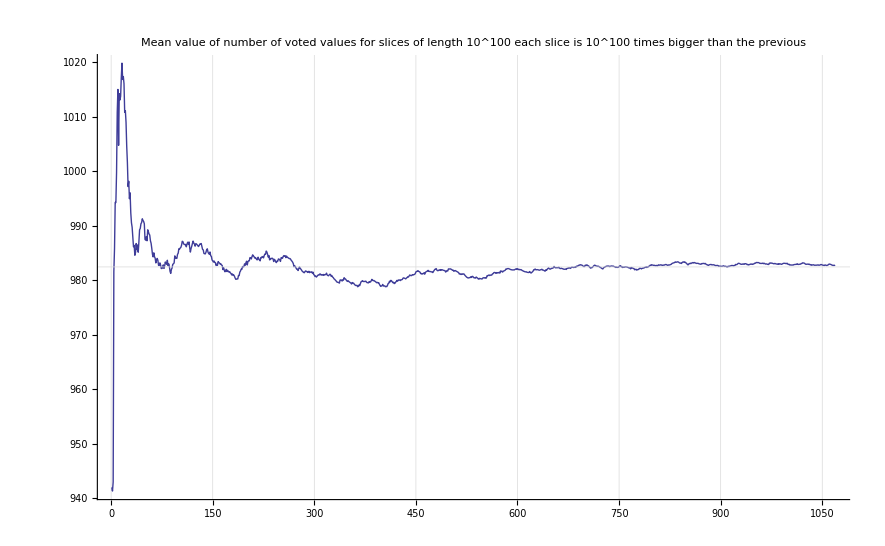

```mathematica
ListPlot[Table[Mean[Take[values-1,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}}, PlotLabel->"Mean value of number of voted values for slices of length 10^100\neach slice is 10^100 times bigger than the previous"]
```

```mathematica
FullSimplify[Log[10,sliceLength]*(Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11])]
```

(Log[18480] Log[sliceLength])/Log[10]

```mathematica
N[Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11]]
```

9.82444

```mathematica
Mean[values]
```

33457/34

```mathematica
N[Log[3]+Log[5]+Log[7]+Log[11]]
```

7.05186

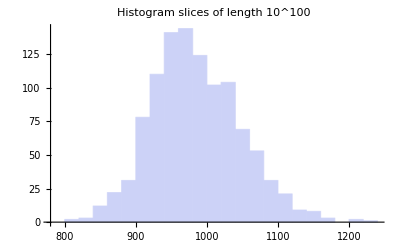

```mathematica
Histogram[values,PlotLabel->"Histogram\nslices of length 10^100"]
```

```mathematica
N[Kurtosis[values]]
```

3.27813

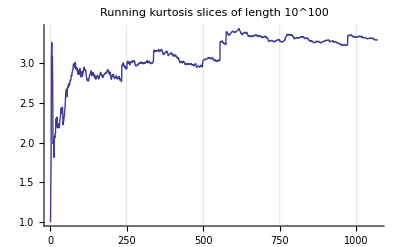

```mathematica
ListPlot[Table[Kurtosis[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}},PlotLabel->"Running kurtosis\nslices of length 10^100"]
```

```mathematica
N[Skewness[values]]
```

0.355026

```mathematica
N[Mean[values]]
```

983.784

```mathematica
N[Variance[values]]
```

3888.71

```mathematica
N[Kurtosis[values]]
```

3.31285

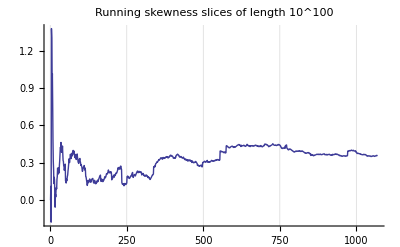

```mathematica
ListPlot[Table[Skewness[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}},PlotLabel->"Running skewness\nslices of length 10^100"]
```

```mathematica
values
```

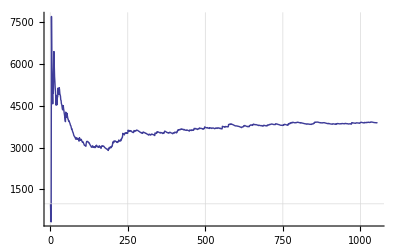

```mathematica
ListPlot[Table[Variance[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}}]
```

```mathematica
values1={921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048}
```

{921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048}

```mathematica
values1={921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048}
```

{921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048}

```mathematica
Length[values1]*10
```

6800

```mathematica
z= Binomial [2 * 3160, 3160]
```

32444190244921375449525053406026907272682306234993552465459504982496116342276252553937060731108974749936394634935314415184777334503602104488596947968124212140080491147999731680509446066143992878895226748409275187362368117059357153916492054714509728688864620311624224670583925791631338421075377510954666558743821153986195288869015960511026239301896555948800499175464712103835625046799714679845007792928694281664496983130462573234518977176872638922286738483090113396479454779416310739151709744123792856935141307438777487628684733230475932239323185963768427370049358287039992872476519806653425144066791724951883992732809138905393738895552536377743358533295361454690801817560713030445346568759457476072057764078340006564869562101252191461620754802462741382343006436398113784275259612450743188894647572910868956918422352141318112901572223863400716522509922058960636607017068396753066241932085168697652190846116133604230420958645877844405070922099631990445229837822337356365355912828281889371390619435197684726552851384925782758013192026109650984377064721933811395187206748528926138125989246331229133331208364814693924696913768604778049158471056711945523445301957485230997379747443260405903862112026480827956787739876314643237823051887914535585124136397318473666923997745352602956793112277943297827060273451496760890749097395629297496808799688578866316065314868024676511732235389935909014541478962496263163766096334740690164753823739729496551260070711555956286892538546265120125835768996752692370684892965843673343004648558649607606091419971372762843656177533047179854584777281406707552949636407167205919501461817414306057664028255518703439343174074261407954147328314844811113236731414263420058511120964028544009169676297478937533715484061094912511704124673882619800254406916695642552127738593869927180190115328393432810476843754144357907071220949304037711865733052891720900621122936092352344677638511536864

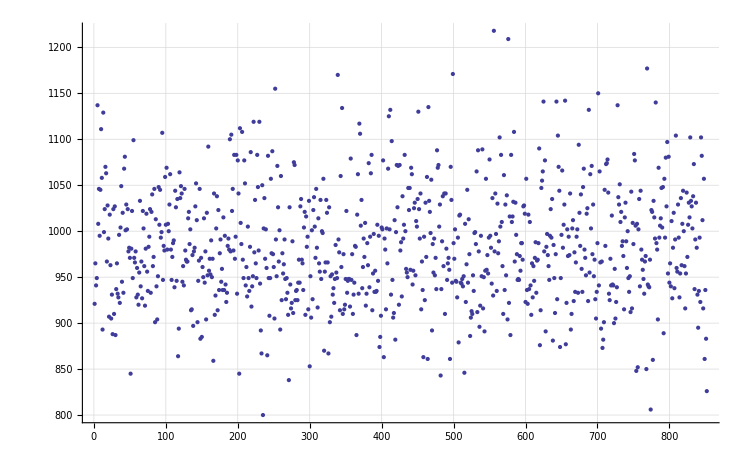

```mathematica
ListPlot[values,GridLines->Automatic]
```

```mathematica
Table[{i,N[CentralMoment[values,i]]},{i,1,5}]
```

{{1,0.},{2,3886.87},{3,87024.7},{4,4.96266×10^7},{5,3.12426×10^9}}

```mathematica
Variance[values]
```

2821493435/725052